## Propeller

```mathematica
domain="Aero";
displayName="Propeller";
brief="Model of a propeller";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[path,domain,displayName];
ResetComponentVariables[]
Date[]
```

```mathematica
inputVariables={
{Up,1.25,double,"m/s","Air speed"},
{rho,1.25,double,"kg/m3","Air density"}
};
```

```mathematica
k=.;
dp=.;
cp=.;
b1=.;
b2=.;
```

```mathematica
inputParameters={
{dp,1.,double,"m","Propeller diameter"},
{b1,0.2,double,"m","Propeller thrust coefficient"},
{b2,0.2,double,"m","Propeller thrust coefficient"},
{g1,0.205,double,"m","Propeller torque coefficient"},
{g2,0.2,double,"m","Propeller torque coefficient"},
{ct0,0.12,double,"m","Propeller torque coefficient"},
{cp0,0.08,double,"m","Propeller torque coefficient"},
{k,4,double,"","exponent for transition"}
};
```

```mathematica
outputVariables={
{thrust,500.,double,"N","Thrust"},
{torque,0.,double,"N","Thrust"},
{Pin,0.,double,"W","Input power"},
{Pout,0.,double,"W","Output Power"},
{Jp,0.,double," ","Advance rate"}
};
```

```mathematica
nodeConnections={
MechanicRotCnode[mr1,0.,0.,"Mechanical rot.connection"]
};
```

```mathematica
b1=.;
b2=.;
g1=.;
g2=.;
ct0=.;
cp0=.;
k=.;
```

```mathematica
ct1=b1-b2 Jpe;
cp1=g1-g2 Jpe;
```

```mathematica
ct:=ct1/Abs[ct1](1/((1/ct0)^k+1/Abs[ct1]^k))^(1/k);
cp:=cp1/Abs[cp1](1/((1/cp0)^k+1/Abs[cp1]^k))^(1/k);
```

```mathematica
b1=0.2;
b2=0.2;
g1=0.205;
g2=0.2;
ct0=0.12;
cp0=0.08;
k=3;
Jpe=.;
```

The trust and power coefficients are plotted below. The curves are symetric although in reality the curves are different abouve Jpe = 1. The normal mode of operation is however, with positive coefficients. The behavior here would be accurate  with a symetric profile.

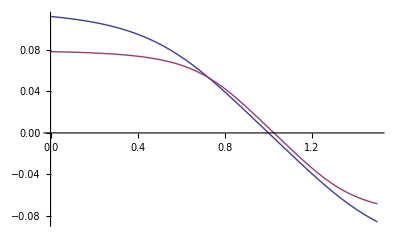

```mathematica
Plot[{ct,cp},{Jpe,0,1.5}]
```

```mathematica
b1=.;
b2=.;
g1=.;
g2=.;
ct0=.;
cp0=.;
k=.;
```

```mathematica
ct
```

((b1-b2 Jpe) (1/((1/ct0)^k+Abs[b1-b2 Jpe]^-k))^(1/k))/Abs[b1-b2 Jpe]

```mathematica
cp
```

((g1-g2 Jpe) (1/((1/cp0)^k+Abs[g1-g2 Jpe]^-k))^(1/k))/Abs[g1-g2 Jpe]

```mathematica
nmp=60 wmr1/(2 pi)
```

9.5493 wmr1

```mathematica
nsp=wmr1/(2 pi)
```

0.159155 wmr1

```mathematica
Jpe=Up/((.00001+nsp) dp)
```

Up/(dp (0.00001+0.159155 wmr1))

```mathematica
systemEquationsDA={
thrust==ct rho nsp^2 dp^4,
cmr1==(cp rho nsp^2 dp^5)/(2 pi)
};
```

```mathematica
systemVariables={thrust,cmr1}
```

{thrust,cmr1}

```mathematica
expressions={
torque==cmr1,
Zcmr1==0.,
Pin==cmr1 wmr1,
Pout==thrust Up,
Jp==Jpe
};
```

```mathematica
Compgen[file]
```